```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Collision*)
κ[α_]:=1/(1+0.715α)(0.715 α+4/27 √(3 α/2));
fstar‵β[vw_]:=0.62/(1.8-0.1vw+vw^2);
fenv[vw_,βH_,T_,gstar_]:=16.5*10^-3*10^-6*fstar‵β[vw]*βH*T/100*(gstar/100)^(1/6);
Senv[f_,vw_,βH_,T_,gstar_]:=(3.8 (f/fenv[vw,βH,T,gstar])^2.8)/(1+2.8(f/fenv[vw,βH,T,gstar])^3.8);
Ωh2cor[f_,vw_,α_,βH_,T_,gstar_]:=1.67*10^-5 βH^-2((κ[α] α)/(1+α))^2(100/gstar)^(1/3)((0.11 vw^3)/(0.42+vw^2))Senv[f,vw,βH,T,gstar];

(*Sound wave*)
κA[vw_,α_]=vw^(6/5)(6.9α)/(1.36-0.037 √α+α);
κB[α_]=α^(2/5)/(0.017+(0.997+α)^(2/5));
κsw[vw_,α_]=Piecewise[{{κA[vw,α] ((1/√3)^(11/5)κB[α])/(((1/√3)^(11/5)-vw^(11/5))κB[α]+vw (1/√3)^(6/5)κA[vw,α]),vw<1/(√3)},{α/(0.73+0.083 √α+α),vw>=1/(√3)}}];
fsw[vw_,βH_,T_,gstar_]=1.9*10^(-5)*(gstar/100)^(1/6)*(T/100)*(βH)/vw;
Htaushock[vw_,α_,βH_]=Min[1,(8π)^(1/3)(Max[vw,1/(√3)]/βH)(4/3(1+α)/(κsw[vw,α] α))^(1/2)];
Ωh2sw[f_,vw_,α_,βH_,T_,gstar_]:=2.65*10^-6 Htaushock[vw,α,βH] 1/βH((κsw[vw,α]α)/(1+α))^2(100/gstar)^(1/3)vw(f/fsw[vw,βH,T,gstar])^3(7/(4+3(f/fsw[vw,βH,T,gstar])^2))^(7/2);

(*Turbulence*)
κtur[vw_,α_]=.05*κsw[vw,α];
(*Plasma turbulence*)
ftur[vw_,βH_,T_,gstar_]=2.7/vw*10^-5*βH*(T/100)*(gstar/100)^(1/6);
(*A peak frequency of the turbulence*)
hstar[T_,gstar_]=16.5*10^-6*(T/100)*(gstar/100)^(1/6);
(*Hubble paramter at Subscript[T, n]*)
Ωtur[f_,vw_,α_,βH_,T_,gstar_]:=3.35*10^(-4)/βH*(κtur[vw,α]*α/(1+α))^(3/2)*(100/100)^(1/3)*vw*(f/ftur[vw,βH,T,gstar])^3/(1+f/(ftur[vw,βH,T,gstar]))^(11/3)/(1+8*Pi*f/hstar[T,gstar])
(*GW signal sourced by the plasma turbulence*)

(*Plot*)
Ωtot[f_,vw_,α_,βH_,T_,gstar_]:=Ωh2cor[f,vw,α,βH,T,gstar]+Ωh2sw[f,vw,α,βH,T,gstar]+Ωtur[f,vw,α,βH,T,gstar];
```

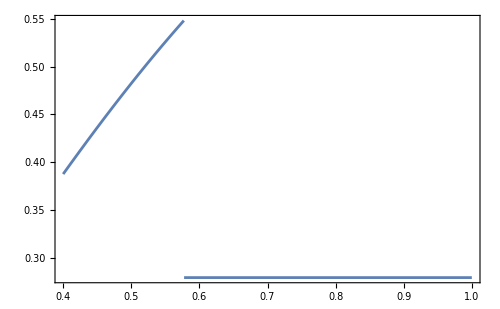

```mathematica
Plot[{κsw[v,0.3]},{v,0.4,1.0}]
```

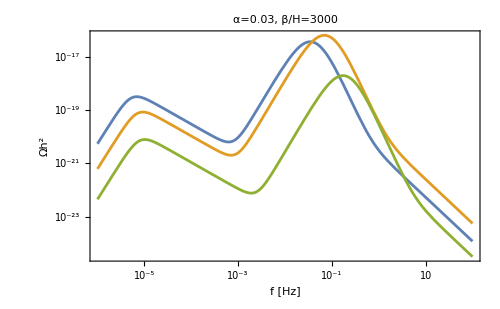

```mathematica
Plot[{Log10[Ωtot[10^lgf,1,0.03,3000,60,106]],Log10[Ωtot[10^lgf,0.5,0.03,3000,60,106]],Log10[Ωtot[10^lgf,0.2,0.03,3000,60,106]]},{lgf,-6,2},FrameTicks->{{LogTicks[-25,-15,2],True},{LogTicks[-7,5,2],True}},Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},{Style["v_w=1",FontFamily->"CMU Serif",FontSize->18],Style["v_w=0.5",FontFamily->"CMU Serif",FontSize->18],Style["v_w=0.2",FontFamily->"CMU Serif",FontSize->18]}]}],RoundingRadius->5],Scaled[{0.2,0.2}]]},FrameLabel->{"f [Hz]","Ωh^2"},PlotLabel->"α=0.03, β/H=3000"]
```

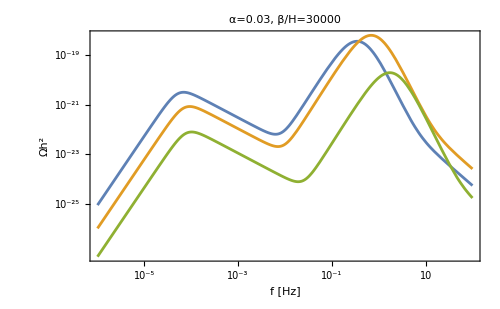

```mathematica
Plot[{Log10[Ωtot[10^lgf,1,0.03,30000,60,106]],Log10[Ωtot[10^lgf,0.5,0.03,30000,60,106]],Log10[Ωtot[10^lgf,0.2,0.03,30000,60,106]]},{lgf,-6,2},FrameTicks->{{LogTicks[-25,-15,2],True},{LogTicks[-7,5,2],True}},Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},{Style["v_w=1",FontFamily->"CMU Serif",FontSize->18],Style["v_w=0.5",FontFamily->"CMU Serif",FontSize->18],Style["v_w=0.2",FontFamily->"CMU Serif",FontSize->18]}]}],RoundingRadius->5],Scaled[{0.2,0.2}]]},FrameLabel->{"f [Hz]","Ωh^2"},PlotLabel->"α=0.03, β/H=30000"]
```